# Equipotential lines. Starter Code

#### Example of setting up a region

{-1+x^2+y^2,-x,-0.5-y}

{-1+x^2+y^2≤0,-x≤0,-0.5-y≤0}

-1+x^2+y^2≤0&&-x≤0&&-0.5-y≤0

ImplicitRegion[-1+x^2+y^2≤0&&-x≤0&&-0.5-y≤0,{x,y}]

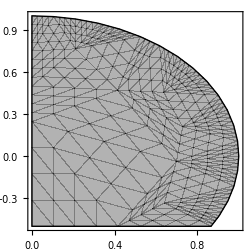

```mathematica
bound = {
x^2+y^2-1 ,
-x ,
-y-0.5
}

boundConditions = Map[#≤ 0&, bound] (* Apply ≤0 condition to all equations *)
boundConditionsAnd= Apply[And,boundConditions] (* Apply 'and' operation to all conditions *)
Ω=ImplicitRegion[boundConditionsAnd , {x, y}] (* Region defined by conditions *)
RegionPlot[Ω] (* plot *)
```

#### Set up boundaries for a region and electrodes

{-y≤0,-1+y≤0,-x≤0,-2.5+x≤0,1/200-(-0.2+x)^2-(-0.5+y)^2≤0,1/200-(-1+x)^2-(-0.5+y)^2≤0,1/5-16. (1/2 √3 (-2+x)+1/2 (-0.38+y))^2-400. (1/2 (-2+x)+1/2 √3 (-0.38+y))^2≤0,1/5-16. (1/2 √3 (-2+x)+1/2 (0.62-y))^2-400. ((2-x)/2+1/2 √3 (-0.62+y))^2≤0,0.8-1111.11 (-2.2+x)^2-16. (-0.5+y)^2≤0}

-y≤0&&-1+y≤0&&-x≤0&&-2.5+x≤0&&1/200-(-0.2+x)^2-(-0.5+y)^2≤0&&1/200-(-1+x)^2-(-0.5+y)^2≤0&&1/5-16. (1/2 √3 (-2+x)+1/2 (-0.38+y))^2-400. (1/2 (-2+x)+1/2 √3 (-0.38+y))^2≤0&&1/5-16. (1/2 √3 (-2+x)+1/2 (0.62-y))^2-400. ((2-x)/2+1/2 √3 (-0.62+y))^2≤0&&0.8-1111.11 (-2.2+x)^2-16. (-0.5+y)^2≤0

ImplicitRegion[-y≤0&&-1+y≤0&&-x≤0&&-2.5+x≤0&&1/200-(-0.2+x)^2-(-0.5+y)^2≤0&&1/200-(-1+x)^2-(-0.5+y)^2≤0&&1/5-16. (1/2 √3 (-2+x)+1/2 (-0.38+y))^2-400. (1/2 (-2+x)+1/2 √3 (-0.38+y))^2≤0&&1/5-16. (1/2 √3 (-2+x)+1/2 (0.62-y))^2-400. ((2-x)/2+1/2 √3 (-0.62+y))^2≤0&&0.8-1111.11 (-2.2+x)^2-16. (-0.5+y)^2≤0,{x,y}]

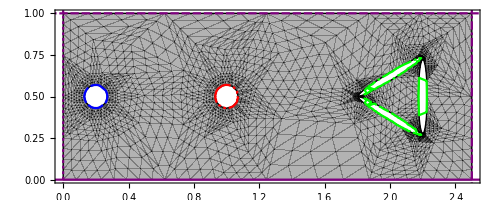

```mathematica
bound={
-y-0, (*bound[[1]]*)
y-1,(*bound[[2]]*)
 0-x, (*bound[[3]]*)
-2.5+x,(*bound[[4]]*)
1/200-(-0.2+x)^2-(y-0.5)^2, (*bound[[5]]*)
1/200-(-1+x)^2-(y-0.5)^2,(*bound[[6]]*)
 1/5-((x-2)Cos[π/6]+(y-0.38)Sin[π/6])^2/0.25^2-((x-2)Sin[π/6]+(y-0.38)Cos[π/6])^2/0.05^2,(*bound[[7]]*)
 1/5-((x-2)Cos[-π/6]+(y-0.62)Sin[-π/6])^2/0.25^2-((x-2)Sin[-π/6]+(y-0.62)Cos[-π/6])^2/0.05^2,(*bound[[8]]*)

 1/1.25-((x-2.2)Cos[π/2]+(y-0.5)Sin[π/2])^2/0.25^2-((x-2.2)Sin[π/2]+(y-0.5)Cos[π/2])^2/0.03^2(*bound[[9]]*)
};

boundConditions = Map[#≤ 0&, bound] (* Apply ≤0 condition to all equations *)
boundConditionsAnd= Apply[And,boundConditions] (* Apply 'and' operation to all conditions *)
Ω=ImplicitRegion[boundConditionsAnd , {x, y}] (* Region defined by conditions *)


Show[RegionPlot[Ω],
ContourPlot[
Evaluate[Thread[bound==0]],{x,-0.1,5},{y,-0.1,2}, (* draw color lines on borders within this ranges of x and y *)
ContourStyle->{Purple,Purple,Purple,Purple,Blue, Red, Green, Green, Green} (* colors for lines *)
],
AspectRatio->Automatic]
```

#### Specify voltage on bound

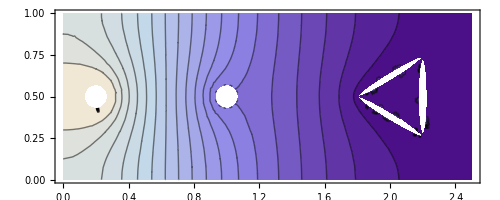

```mathematica
(* If condition for a border not given, potential can have any value there *)

sol =NDSolveValue[{∇_{x,y}^2 u[x,y]==0,
{DirichletCondition[u[x,y]==5,bound[[5]]==0],
DirichletCondition[u[x,y]==0,bound[[6]]==0],
DirichletCondition[u[x,y]==-2,bound[[7]]==0],
DirichletCondition[u[x,y]==-2,bound[[8]]==0],
DirichletCondition[u[x,y]==-2,bound[[9]]==0]
}},u,{x,y}∈Ω];

ContourPlot[sol[x,y],{x,y}∈Ω,Mesh->None,
ColorFunction-> "Electric Potential Map",
Contours -> 18,AspectRatio->Automatic]
```